# Rules and Patterns Part 2

## Basic Exercises

### Question Subsection

Use PatternTest to highlight all the prime numbers in the list of integers smaller than 100.

#### Solution

```mathematica
Range[100]/.{n_Integer?PrimeQ->Framed[n,Background->Yellow]}
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

### Question Subsection

Highlight the prime numbers in the sequence of first 100 Fibonacci numbers.

#### Solution

```mathematica
Table[Fibonacci[n],{n,100}]/.{n_?EvenQ->Framed[n,Background->Yellow]}
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040,1346269,2178309,3524578,5702887,9227465,14930352,24157817,39088169,63245986,102334155,165580141,267914296,433494437,701408733,1134903170,1836311903,2971215073,4807526976,7778742049,12586269025,20365011074,32951280099,53316291173,86267571272,139583862445,225851433717,365435296162,591286729879,956722026041,1548008755920,2504730781961,4052739537881,6557470319842,10610209857723,17167680177565,27777890035288,44945570212853,72723460248141,117669030460994,190392490709135,308061521170129,498454011879264,806515533049393,1304969544928657,2111485077978050,3416454622906707,5527939700884757,8944394323791464,14472334024676221,23416728348467685,37889062373143906,61305790721611591,99194853094755497,160500643816367088,259695496911122585,420196140727489673,679891637638612258,1100087778366101931,1779979416004714189,2880067194370816120,4660046610375530309,7540113804746346429,12200160415121876738,19740274219868223167,31940434634990099905,51680708854858323072,83621143489848422977,135301852344706746049,218922995834555169026,354224848179261915075}

### Question Subsection

Use combination of Cases with PatternTest or PatternCondition to pick numbers below 100 whose binary representation are a palindrome.

#### Hint

A palindrome is a phrase or a number that is the same forwards and backwards. You can use PalindromeQ to test for this condition. 
In order to find the binary representation of a number, you can use IntegerDigits function.

#### Solution

```mathematica
Column@Cases[Table[n,{n,100}],n_Integer/;PalindromeQ[IntegerDigits[n,2]]->Grid[{{n,Row@IntegerDigits[n,2]}},Frame->All]]
```

1 | 1
3 | 11
5 | 101
7 | 111
9 | 1001
15 | 1111
17 | 10001
21 | 10101
27 | 11011
31 | 11111
33 | 100001
45 | 101101
51 | 110011
63 | 111111
65 | 1000001
73 | 1001001
85 | 1010101
93 | 1011101
99 | 1100011

## Intermediate Exercises

### Question Subsection

In the following figure, use Condition to redraw the circles whose radii are even with thick and red lines.

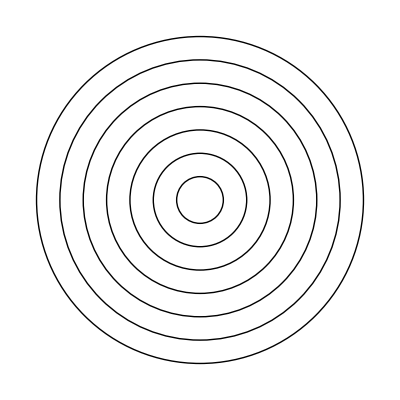

```mathematica
Graphics[Table[Circle[{0,0},r],{r,1,7,1}]]
```

#### Hint

In order to check if a number n is even, you can use Mod[n,2]==0.

#### Solution

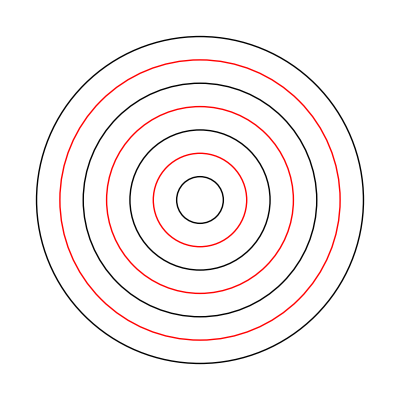

```mathematica
Graphics[Table[Circle[{0,0},r],{r,1,7,1}]]/.{Circle[{0,0},r_/;Mod[r,2]==0]->{Red,Thick,Circle[{0,0},r]}}
```

### Question Subsection

Use Cases with a combination of PatternTest and Condition to group all the prime numbers smaller than 500 into bins of width 10, i.e. all the primes between 1 and 10, in one bin (list), primes between 11 and 20 in the next, and so on.

#### Hint

You will need to use the Table function here. 
In order to test two conditions at once, you can use &&. For example if you want to check to see if a number n is between 0 and 10, you would do n>0 && n<10. Alternatively, you can chain the tests as we saw in the lecture.

#### Solution

```mathematica
talliedprimes=Table[Cases[Range[500],(n_?PrimeQ)/;n>i && n<i+10],{i,0,490,10}]
```

{{2,3,5,7},{11,13,17,19},{23,29},{31,37},{41,43,47},{53,59},{61,67},{71,73,79},{83,89},{97},{101,103,107,109},{113},{127},{131,137,139},{149},{151,157},{163,167},{173,179},{181},{191,193,197,199},{},{211},{223,227,229},{233,239},{241},{251,257},{263,269},{271,277},{281,283},{293},{307},{311,313,317},{},{331,337},{347,349},{353,359},{367},{373,379},{383,389},{397},{401,409},{419},{421},{431,433,439},{443,449},{457},{461,463,467},{479},{487},{491,499}}

### Question Subsection

Use the list you produced above to display the length of each bin in a row. Style this number to reflect its magnitude. For the bins that have no elements, put a red disk. We are aiming for something similar to the following image.

#### Solution

```mathematica
Row@talliedprimes/.{l:{__Integer}:>Style[Length[l],10*Length[l]],l_List/;Length[l]==0->Graphics[{Red,Disk[]},ImageSize->10]}
```

44223223214113122214-Graphics-13212222113-Graphics-22212212113213112

## Advanced Exercises

```mathematica
DataBase={
"Jalanda"->{"Age"-> 27,"State"->"PA", "Gender"->"F"},
"Jack"->{"Age"-> 54,"State"->"CA", "Gender"->"M"},
"Jake"->{"Age"-> 34,"State"->"MD", "Gender"->"M"},
"Jane"->{"Age"-> 14,"State"->"PA", "Gender"->"F"},
"Jeremiah"->{"Age"-> 57,"State"->"PA", "Gender"->"M"},
"Jodie"->{"Age"-> 39,"State"->"FL", "Gender"->"F"},
"Joe"->{"Age"-> 37,"State"->"PA", "Gender"->"M"},
"John"->{"Age"-> 23,"State"->"IL", "Gender"->"M"},
"Judy"->{"Age"-> 43,"State"->"PA",  "Gender"->"F"}
};
```

### Question Subsection

In the database above, count how many people live in the state of Pennsylvania (PA).

#### Solution

```mathematica
Count[DataBase,Rule[_,{___,Rule["State","PA"],___}]]
```

5

### Question Subsection

List the names all the girls who are older than 30. You can use Cases for this.

#### Solution

```mathematica
Cases[DataBase,Rule[name_,{___,Rule["Age",a_/;a>30],___,Rule["Gender","F"],___}]->name]
```

{Jodie,Judy}